## Fitting parameters in W1 and W2 approaches

```mathematica
ClearAll["Global`*"]
```

```mathematica
path[filename_]:=StringTemplate["/Users/basavyr/Documents/Work/PhD/163Lu-New-TSD4-Formalism/Code/Update-July-2022/plots/``.pdf"][filename];
export[filename_,obj_]:=Export[path[filename],Show[obj]];
```

```mathematica
moiW1={63.2,20,10};
moiW1tsd4={67,34.5,50};
moiW2={72,15,7};
VW1=3.1;
VW1tsd4=0.7;
gmW1=17;
VW2=2.1;
gmW2=22;
```

## MOI ratios

```mathematica
r12w2=N[moiW2[[1]]/moiW2[[2]]]
r13w2=N[moiW2[[1]]/moiW2[[3]]]
r12w1=N[moiW1[[1]]/moiW1[[2]]]
r13w1=N[moiW1[[1]]/moiW1[[3]]]
```

4.8

10.2857

3.16

6.32

## MOI Plots

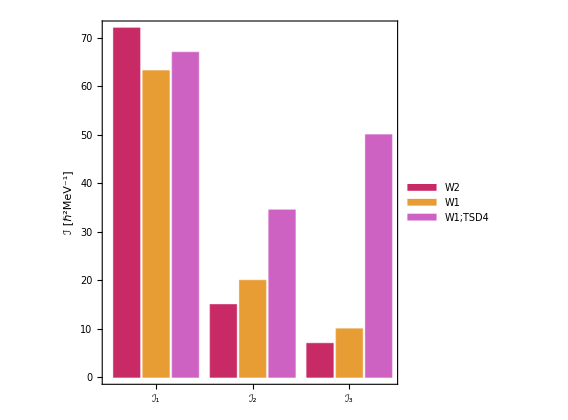

```mathematica
mois=BarChart[{{moiW2[[1]],moiW1[[1]],moiW1tsd4[[1]]},{moiW2[[2]],moiW1[[2]],moiW1tsd4[[2]]},{moiW2[[3]],moiW1[[3]],moiW1tsd4[[3]]}},AspectRatio->1,Frame->True,Axes->False,PlotRange->Full,FrameStyle->Directive[Black,Thick],ImageSize->420,FrameLabel->{None,"ℐ [ℏ^2MeV^-1]"},LabelStyle->{22,Black,FontFamily->"Times"},BarSpacing->Automatic,ChartLegends->Placed[{"W2","W1","W1;TSD4"},{0.7,0.8}],FrameTicks->{{Automatic,Automatic},{Automatic,None}},ChartStyle->54,ChartLabels->{{"ℐ_1","ℐ_2","ℐ_3"},None}];
Show[mois]
export["W1-W2-Mois",mois];
```

```mathematica
(*ChartLabels->{Placed[{Style["ℐ_1",16,Black,Bold],Style["ℐ_2",16,Black,Bold],Style["ℐ_3",16,Black,Bold]},Center]}*)
```